F. Fasso`.    Universita` di Padova.    Laurea in Matematica.   Esercizi per il corso di Laboratorio Computazionale, a.a. 2019-20

# Qualche esercizio sulle lezioni 1-4

Esercizi semplici ed opzionali; le soluzioni non vanno consegnati per l’esame.

1. Creare una lista che contiene i quadrati dei numeri naturali fra 1 e 99. Estrarne poi l’undicesimo elemento.

```mathematica
r =Range[99]^2
```

{1,4,9,16,25,36,49,64,81,100,121,144,169,196,225,256,289,324,361,400,441,484,529,576,625,676,729,784,841,900,961,1024,1089,1156,1225,1296,1369,1444,1521,1600,1681,1764,1849,1936,2025,2116,2209,2304,2401,2500,2601,2704,2809,2916,3025,3136,3249,3364,3481,3600,3721,3844,3969,4096,4225,4356,4489,4624,4761,4900,5041,5184,5329,5476,5625,5776,5929,6084,6241,6400,6561,6724,6889,7056,7225,7396,7569,7744,7921,8100,8281,8464,8649,8836,9025,9216,9409,9604,9801}

```mathematica
r[[11]]
```

121

2. Definire una funzione f(n) che produce la approssimazione di  √3-1 con n cifre decimali

```mathematica
ν[n_] := N[√3-1,n]
```

```mathematica
ν[10]
```

0.7320508076

3. Determinare gli zeri del polinomio  x^3-2x+1

```mathematica
x/.Solve[x^3-2x+1==0]
```

{1,1/2 (-1-√5),1/2 (-1+√5)}

4. Quanto e` lunga un’ellisse di semiassi  a=2 e b=1?  
[Suggerimenti: una parametrizzazione dell’ellisse e`
       t →   (a  cos(t) , b sin(t) )  0≤ t≤2π
Ricordare poi che la lunghezza di tale curva e` l’integrale fra t_0 e t_1 della norma ||γ’(t)|| = √(x'(t)^2+y'(t)^2) della derivata (o vettore tangente) γ’(t) =  (x’(t),y’(t)). Si puo` fare il calcolo numerico con NIntegrate. Se serve, consultare l’help per sapere come si calcola un integrale definito.]

```mathematica
x[t_]:=2Cos[t]; y[t_] := Sin[t];
```

```mathematica
NIntegrate[√((D[x[t],t])^2+(D[y[t],t])^2),{t,0,2π}]
```

9.68845

5. Calcolare l’area di un’ellisse di semiassi a e b. 
[Suggerimenti: se l’equazione cartesiana dell’ellisse e` A x^2+B y^2=1, l’area e` il doppio dell’integrale fra -1/√A e 1/√A della funzione √((1-A x^2)/B).  Il risultato dovrebbe essere  πAB, ma Mathematica  lo da` un po’ piu` complicato (ci sarebbero delle semplificazioni da fare, che non fa perche` non sa se  A e B siano numeri positivi. Per fare la semplificazione usare Assuming --- oppure Assumptions, che potete guardare sull’help)

```mathematica
Assuming[A>0&&B>0 , Simplify [2Integrate[√((1-A x^2)/B),{x,-1/(√A),1/(√A)}]]] (*l'area è πab, dove chiaramente a = 1/(√A) , b = 1/(√B) *)
```

π/(√(A B))

6. Scrivere una funzione che crea la lista dei primi n numeri naturali dispari. Fare poi il grafico di tale lista per n=11, unendone i punti con segmenti.
[Suggerimenti: ListPlot, Opzione Joined]

```mathematica
disp[m_] := Table[2k+1,{k,0,m}];
```

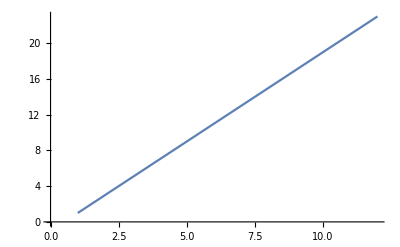

```mathematica
ListPlot[disp[11],Joined->True]
```

7. Scrivere  (in tre modi diversi) una funzione che disegna un’ellisse di semiassi a e b : 
    - come curva parametrizzata
    - come curva di livello di una funzione
    - come (unione) di grafici di due funzioni
Trattare a e b come parametri:
     PlotEll[a_,b_]:= .....

Suggerimenti:
- la parametrizzazione cartesiana dell'ellisse e`  γ(t) = (a  cos(t) , b sin(t) ) , 0≤ t≤2π
- l'equazione cartesiana dell'ellisse e`   x^2/a^2+y^2/b^2=1  ;  per fare un ContourPlot bisogna stabilire in quale intervallo varia  x 
- le due funzioni sono  y_+(x) = √(....)  e y_-(x) = -√(....)

```mathematica
EllParam[a_,b_] := ParametricPlot[{a Cos[t],b Sin[t]},{t,0,2π}]
```

```mathematica
EllLiv[a_ ,b_] := ContourPlot[(x/a)^2+(y/b)^2==1,{x,-a,a},{y,-b,b}]
```

```mathematica
EllGraph[a_,b_]:=Plot[{√(b(1-(x/a)^2)),-√(b(1-(x/a)^2))},{x,-a,a}]
```

8. Disegnare una sfera in due modi:
    - come superficie parametrizzata
    - come insieme di livello di una funzione

```mathematica
ParametricPlot3D[{Sin[ϕ]Cos[θ],Sin[ϕ]Sin[θ],Cos[ϕ]},{ϕ,0,π},{θ,0,2π}]
```

-Graphics3D-

```mathematica
ContourPlot3D[x^2+y^2+z^2==1,{x,-1,1},{y,-1,1},{z,-1,1}]
```

-Graphics3D-

9. Una parametrizzazione di un nastro di Moebius è data da

(s,φ)→ (Cos[φ] | -Sin[φ] | 0
Sin[φ] | Cos[φ] | 0
0 | 0 | 1)(R+s Cos[φ/2]
0
s Sin[φ/2])

con s∈ [-r,r] e  φ ∈ [0,2π] (ove R > r sono due parametri che si possono scegliere a piacere). Disegnare un nastro di Moebius

```mathematica
M[θ_]:= {{Cos[θ],-Sin[θ],0},{Sin[θ],Cos[θ],0},{0,0,1}}
```

```mathematica
v[R_,s_,θ_]:= {R+s Cos[θ/2],0,s Sin[θ/2]}
```

```mathematica
ParametricPlot3D[M[θ].v[2,s,θ],{s,-1,1},{θ,0,2π}]
```

-Graphics3D-

10. Una possibile immersione non-iniettiva della bottiglia di Klein in R^3 è data da
            -Graphics-
Disegnarla, cercando di evidenziare le autointersezioni.

```mathematica
x[ϕ_,θ_] := (3+Cos[θ/2]Sin[ϕ]-Sin[θ/2]Sin[2ϕ])Cos[θ]
```

```mathematica
y[ϕ_,θ_] := (3+Cos[θ/2]Sin[ϕ]-Sin[θ/2]Sin[2ϕ])Sin[θ]
```

```mathematica
z[ϕ_,θ_]:=Sin[θ/2]Sin[ϕ]+Cos[θ/2]Sin[2ϕ]
```

```mathematica
ParametricPlot3D[{x[f,t],y[f,t],z[f,t]},{f,0,2π},{t,0,2π},PlotStyle->Opacity[0.5],Mesh->None,BoundaryStyle->Red]
```

-Graphics3D-